## 2-dimensional vertex model :> simulating epithelial tissue

```mathematica
LaunchKernels[]
ParallelTable[$KernelID,{i,$KernelCount}]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

{6,5,4,3,2,1}

## geometrical f(x)s

```mathematica
(*get vertex in the list by ccw order*)
Clear[getCounterClockwise];
getCounterClockwise[vertex_,vertices_]:=Block[{pos,v},
pos=First@@Position[vertices,vertex];
If[pos==Length[vertices],pos=1,pos+=1];
vertices[[pos]]
];
```

```mathematica
(*get vertex in the list by cw order*)
Clear[getClockwise];
getClockwise[vertex_,vertices_]:=Block[{ls,pos},
pos=First@@Position[vertices,vertex];
If[pos==1,pos=Length[vertices],pos-=1];
vertices[[pos]]
];
```

```mathematica
getCounterClockwise[{Subscript[x, i],Subscript[y, i]},{{Subscript[x, i-1],Subscript[y, i-1]},{Subscript[x, i],Subscript[y, i]},{Subscript[x, i+1],Subscript[y, i+1]},d,e}]
```

{x_(1+i),y_(1+i)}

```mathematica
getClockwise[{Subscript[x, i],Subscript[y, i]},{{Subscript[x, i-1],Subscript[y, i-1]},{Subscript[x, i],Subscript[y, i]},{Subscript[x, i+1],Subscript[y, i+1]},d,e}]
```

{x_(-1+i),y_(-1+i)}

```mathematica
Clear[areaOfPolygon];
areaOfPolygon[cells_/;Head[cells]===Association]:=Parallelize[Map[Area@*Polygon,cells]];
```

```mathematica
Clear[areaPolygon];
areaPolygon[vertices_]:=Block[{edges},
edges=Partition[vertices,2,1,1];
0.5Abs@Total[(#[[1,1]]*#[[2,2]])-(#[[2,1]]*#[[1,2]])&/@edges]
]
```

```mathematica
Clear[perimeterOfPolygon];
perimeterOfPolygon[cells_/;Head[cells]===Association]:=Parallelize[(Perimeter@*Polygon)/@cells];
```

```mathematica
Clear[perimeterPolygon];
perimeterPolygon[vertices_]:=Block[{edges},
edges=Partition[vertices,2,1,1];
Total[Apply[EuclideanDistance]/@edges]
]
```

```mathematica
Clear[centroidPolygon];
centroidPolygon[vertices_]:=Mean[vertices]
```

```mathematica
(*counterclockwise polygonQ*)
Block[{signedarea=0,j,vertlen=5},
Do[
j=Mod[i,vertlen]+1;
signedarea+= (Subscript[x, i] Subscript[y, j]-Subscript[x, j] Subscript[y, i]),
{i,vertlen}];
Echo[1/2(signedarea)]
];
```

1/2 (-x_2 y_1+x_5 y_1+x_1 y_2-x_3 y_2+x_2 y_3-x_4 y_3+x_3 y_4-x_5 y_4-x_1 y_5+x_4 y_5)

```mathematica
Clear[polyCounterClockwiseQ];
polyCounterClockwiseQ[poly_]:=Block[{area=0,j,vertLength=Length[poly]},
Do[
j=Mod[i,vertLength]+1;
area+= poly[[i,1]]*poly[[j,2]];
area-= poly[[j,1]]*poly[[i,2]],
{i,vertLength}
];
(area/2.)>0
]
```

```mathematica
(*Clear[sortCC];
sortCC[polyinds_,indTopts_,ptsToInds_]:=Block[{cent,poly},
poly=Lookup[indTopts,polyinds];
Lookup[ptsToInds,
DeleteDuplicates@Flatten[MeshPrimitives[ConvexHullMesh[poly],1]/.Line->Sequence,1]
]
];*)
```

```mathematica
(*sort points for a convex polygon in counter-clockwise direction*)
```

```mathematica
Clear[sortPointsCC];
sortPointsCC[polyinds_,indTopts_,ptsToInds_]:=Block[{cent,ordering,polyPoints},
polyPoints=Lookup[indTopts,polyinds];
cent=Mean[polyPoints];
ordering=Ordering[ArcTan[#[[1]],#[[2]]]&@(#-cent)&/@polyPoints];
Lookup[ptsToInds,Part[polyPoints,ordering]]
]
```

```mathematica
outeredges[indToPtsAssoc_,localtopology_]:=Block[{k,temp,tcells,assoc},
Reap[
Scan[(k=#;temp=localtopology[k];
tcells=temp[[2]];
If[tcells≠{},
MapAt[Sow@Cases[Partition[#,2,1,1],OrderlessPatternSequence[{x:indToPtsAssoc[k],y:_}]:>{x,y}]&,temp[[1]],{Key[#]}&/@tcells];
])&,Keys@indToPtsAssoc]
][[2]]//Flatten[#,2]&
];
```

## mesh restructuring operations

simulation domain

```mathematica
xLim=yLim={-1,1};
𝒟=Rectangle[{First@xLim,First@yLim},{Last@xLim,Last@yLim}];
```

### local topology

```mathematica
ClearAll[periodicRules,transformRules];
periodicRules::Information="shift the points outside the simulation domain to inside the domain";
transformRules::Information="vector that shifts the point outside the simulation domain back inside";
With[{xlim1=xLim[[1]],xlim2= xLim[[2]],ylim1= yLim[[1]],ylim2= yLim[[2]],dstep=2},
periodicRules=Dispatch[{
{x_/;x≥xlim2,y_/;y≤ylim1}:>SetPrecision[{x-dstep,y+dstep},10],
{x_/;x≥xlim2,y_/;ylim1<y<ylim2}:>SetPrecision[{x-dstep,y},10],
{x_/;xlim1<x<xlim2,y_/;y≤ylim1}:>SetPrecision[{x,y+dstep},10],
{x_/;x≤xlim1,y_/;y≤ylim1}:>SetPrecision[{x+dstep,y+dstep},10],
{x_/;x≤xlim1,y_/;ylim1<y<ylim2}:>SetPrecision[{x+dstep,y},10],
{x_/;x≤xlim1,y_/;y≥ylim2}:>SetPrecision[{x+dstep,y-dstep},10],
{x_/;xlim1<x<xlim2,y_/;y≥ylim2}:>SetPrecision[{x,y-dstep},10],
{x_/;x≥xlim2,y_/;y≥ylim2}:>SetPrecision[{x-dstep,y-dstep},10]
}];

transformRules=Dispatch[{
{x_/;x≥xlim2,y_/;y≤ylim1}:>{-dstep,dstep}~SetPrecision~10,
{x_/;x≥xlim2,y_/;ylim1<y<ylim2}:>{-dstep,0}~SetPrecision~10,
{x_/;xlim1<x<xlim2,y_/;y≤ylim1}:>{0,dstep}~SetPrecision~10,
{x_/;x≤xlim1,y_/;y≤ylim1}:>{dstep,dstep}~SetPrecision~10,
{x_/;x≤xlim1,y_/;ylim1<y<ylim2}:>{dstep,0}~SetPrecision~10,
{x_/;x≤xlim1,y_/;y≥ylim2}:>{dstep,-dstep}~SetPrecision~10,
{x_/;xlim1<x<xlim2,y_/;y≥ylim2}:>{0,-dstep}~SetPrecision~10,
{x_/;x≥xlim2,y_/;y≥ylim2}:>{-dstep,-dstep}~SetPrecision~10,
{___Real}:>{0,0}~SetPrecision~10}];
];
```

```mathematica
Clear@getLocalTopology;
getLocalTopology[ptsToIndAssoc_,indToPtsAssoc_,vertexToCell_,cellVertexGrouping_,wrappedMat_,faceListCoords_][vertices_]:=Block[{localtopology=<||>,wrappedcellList={},vertcellconns,localcellunion,v,wrappedcellpos,vertcs=vertices,rl1,rl2,
transVector,wrappedcellCoords,wrappedcells,vertOutofBounds,shiftedPt,transvecList={},$faceListCoords=faceListCoords,
vertexQ,boundsCheck,rules,extractcellkeys,vertind,cellsconnected,wrappedcellsrem},
vertexQ=MatchQ[vertices,{__?NumberQ}];
If[vertexQ,
(vertcellconns=AssociationThread[{#} ,{vertexToCell[ptsToIndAssoc[#]]}]&@vertices;
vertcs={vertices};
localcellunion=Flatten[Values@vertcellconns]),
(vertcellconns=AssociationThread[# ,Lookup[vertexToCell,Lookup[ptsToIndAssoc,#]]]&@vertices; 
localcellunion=Union@Flatten[Values@vertcellconns])
];
If[localcellunion≠ {},
AppendTo[localtopology,
Thread[localcellunion->Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping/@localcellunion,{2}]]
]
];
(* condition to be an internal edge: both vertices should have 3 neighbours *)
(* if a vertex has 3 cells in its local neighbourhood then the entire network topology about the vertex is known -> no wrapping required *)
(* else we need to wrap around the vertex because other cells are connected to it -> periodic boundary conditions *)
With[{vert=#},
vertind=ptsToIndAssoc[vert];
cellsconnected=vertexToCell[vertind];
If[Length[cellsconnected]≠3,
If[(𝒟~RegionMember~vert),
v=vert;
With[{x=v[[1]],y=v[[2]]},boundsCheck=(x==xLim[[1]]||x==xLim[[2]]||y==yLim[[1]]||y==yLim[[2]])];
extractcellkeys=If[boundsCheck,
{rl1,rl2}={v,v/.periodicRules};
rules=Block[{x$},
With[{r=rl1,s=rl2},
DeleteDuplicates[HoldPattern[SameQ[x$,r]]||HoldPattern[SameQ[x$,s]]]
]
];
Position@@With[{rule=rules},Hold[wrappedMat,x_/;ReleaseHold@rule,{2}]],
Position[wrappedMat,x_/;SameQ[x,v],{2}]
];
(* find cell indices that are attached to the vertex in wrappedMat *)
wrappedcellpos=DeleteDuplicatesBy[
Cases[extractcellkeys,
{Key[p:Except[Alternatives@@Join[localcellunion,Flatten@wrappedcellList]]],y__}:>{p,y}],
First];
(*wrappedcellpos = wrappedcellpos/.{Alternatives@@Flatten[wrappedcellList],__} :> Sequence[];*)
(* if a wrapped cell has not been considered earlier (i.e. is new) then we translate it to the position of the vertex *)
If[wrappedcellpos≠{},
If[vertexQ,
transVector=SetPrecision[(v-Extract[$faceListCoords,Replace[#,{p_,q__}:> {Key[p],q}]])&/@wrappedcellpos,10],
(* call to function is enquiring an edge and not a vertex*)
transVector=SetPrecision[(v-Extract[$faceListCoords,Replace[#,{p_,q__}:> {Key[p],q}]])&/@wrappedcellpos,10]
];
wrappedcellCoords=MapThread[#1-> Map[Function[x,SetPrecision[x+#2,10]],$faceListCoords[[Key@#1]],{1}]&,
{First/@wrappedcellpos,transVector}];
wrappedcells= Keys@wrappedcellCoords;
AppendTo[wrappedcellList,Flatten@wrappedcells];
AppendTo[transvecList,transVector];
AppendTo[localtopology,wrappedcellCoords]; 
],
(* the else clause: vertex is out of bounds *)
vertOutofBounds=vert;
(* translate the vertex back into mesh *)
transVector=vertOutofBounds/.transformRules;
shiftedPt= SetPrecision[vertOutofBounds+transVector,10];
(* ------------- CORE B ------------- *)
(* find which cells the shifted vertex is a part of in the wrapped matrix *)
wrappedcells=Complement[
Union@Cases[Position[wrappedMat,x_/;SameQ[x,shiftedPt],{2}],
x_Key:>Sequence@@x,{2}]/.Alternatives@@localcellunion-> Sequence[],
Flatten@wrappedcellList];
(*forming local topology now that we know the wrapped cells *)
If[wrappedcells≠{},
AppendTo[wrappedcellList,Flatten@wrappedcells];
wrappedcellCoords=AssociationThread[wrappedcells,
Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#]&/@wrappedcells,{1}]];
With[{opt=(vertOutofBounds/.periodicRules)},
Block[{pos,vertref,transvec},
Do[
With[{cellcoords=wrappedcellCoords[cell]},
pos=FirstPosition[cellcoords/.periodicRules,opt];
vertref=Extract[cellcoords,pos];
transvec=SetPrecision[vertOutofBounds-vertref,10];
AppendTo[transvecList,transvec];
AppendTo[localtopology,cell-> Map[SetPrecision[#+transvec,10]&,cellcoords]];
],{cell,wrappedcells}]
];
];
];
(* to detect wrapped cells not detected by CORE B*)
(* ------------- CORE C ------------- *)
Block[{pos,celllocs,ls,transvec,assoc,tvecLs={},ckey},
ls=Union@Flatten@Join[cellsconnected,wrappedcells];
If[Length[ls]≠ 3,
pos=Position[$faceListCoords,x_/;SameQ[x,shiftedPt],{2}];
celllocs=DeleteDuplicatesBy[Cases[pos,Except[{Key[Alternatives@@ls],__}]],First]/.{Key[x_],z__}:> {Key[x],{z}};
If[celllocs≠{},
celllocs=Transpose@celllocs;
assoc=<|
MapThread[
(transvec=SetPrecision[vertOutofBounds-Extract[$faceListCoords[Sequence@@#1],#2],10];
ckey=Identity@@#1;
AppendTo[tvecLs,transvec];
ckey->Map[SetPrecision[Lookup[indToPtsAssoc,#]+transvec,10]&,cellVertexGrouping[Sequence@@#1],{1}]
)&,celllocs]
|>;
AppendTo[localtopology,assoc];
AppendTo[wrappedcellList,Keys@assoc];
AppendTo[transvecList,tvecLs];
];
];
];
];
];
]&/@vertcs;
transvecList=Which[
MatchQ[transvecList,{{{__?NumberQ}}}],First[transvecList],
MatchQ[transvecList,{{__?NumberQ}..}],transvecList,
True,transvecList//.{x___,{p:{__?NumberQ}..},y___}:>{x,p,y}
];
{localtopology,Flatten@wrappedcellList,transvecList}
];
```

### T1 transition

```mathematica
(*find edge function*)
```

#### find edges

```mathematica
Clear@edgesforT1;
edgesforT1[edgeLs_,indToPts_,threshLength_:0.0015]:=Block[{edges,dist,sel,filt,b,cand,sameedg2Q,del},
edges=Lookup[indToPts,#]&/@edgeLs;
dist=EuclideanDistance@@#&/@edges;
sel=Pick[edges,Thread[dist≤threshLength],True];
If[Length[sel]==1,
Nothing,
filt=sel/.periodicRules;
b=MapThread[SameQ,{filt,sel}];
cand=Pick[filt,b,False];
sameedg2Q=MemberQ[sel,{OrderlessPatternSequence@@#}]&/@cand;
del=(OrderlessPatternSequence@@@Pick[cand,sameedg2Q]);
If[Length[cand]>1,del=Alternatives@@del];
sel=DeleteCases[sel,{del}]
];
sel
];
```

#### T1

```mathematica
bagged=CreateDataStructure["DynamicArray"]
```

DataStructure[DynamicArray, {Data -> {}}]

```mathematica
Clear@T1transitionFn;
T1transitionFn[edges_,indToPtsAssoc_,ptsToIndAssoc_,vertexToCellG_,cellToVertexG_,wrappedMat_,faceListCoords_,dSep_:0.004]:=Block[{edgeind,connectedcellKeys,edge,newpts,cellvertices,pos,cellpolys,memF,keyscellP,selcellKeys,ptToCell,newptsindices,indToPts=indToPtsAssoc,ptsToInds=ptsToIndAssoc,PtIndToCell,keysToMap,f1,otherkeys,f2,bag=bagged,vertToCellG=vertexToCellG,cellToVertG=cellToVertexG,testpts,localtopology,translCells,transVector,edgepts,celltopo,polysharingEdge,ls,cs,cc,ccw,trimmedtopo,ordering,edgeordered,topotransl,newtransvert,findEdges,$wrappedMat=wrappedMat,$faceListCoords=faceListCoords,cellToVertGC,dropinds,bagopen,maxlab,mm,ll},
findEdges=edgesforT1[edges,indToPts];
(* finding all possible edges for T1 transition *)
If[findEdges≠{},
(*run if there are any edges for T1*)
Scan[
(edge=#;
cellToVertGC=cellToVertG;
edgeind=Lookup[ptsToInds,edge];
If[ContainsAll[Keys[indToPts],edgeind],
(* should be an edge not connected to an edge that has already undergone a T1 *)
(* let us get the local network topology *)
{localtopology,translCells,transVector}=getLocalTopology[ptsToInds,indToPts,vertToCellG,cellToVertG,$wrappedMat,$faceListCoords][#]&[edge];
If[!DuplicateFreeQ[translCells],
{translCells,transVector}=DeleteDuplicates[Transpose[{translCells,transVector}]]ᵀ
];
connectedcellKeys=Keys@localtopology;
celltopo=Values@localtopology;
newpts=With[{midPt=Mean@edge},
SetPrecision[midPt+dSep Normalize[(#-midPt)],10]&/@Flatten[RotationTransform[-π/2,midPt]/@{edge},1]
];
testpts=With[{midPt=Mean@edge},midPt+0.00001Normalize[(#-midPt)]&/@newpts];
(*plt1=Graphics[{{FaceForm[LightGray],EdgeForm[{Thick,Black}],Polygon/@celltopo},{Red,Line@edge,Orange,Point@newpts,Green,Point@testpts}},ImageSize->Tiny];
Print@plt1;*)
(*which cells contain both vertices*)
pos=Position[celltopo,{OrderlessPatternSequence[___,First[edge],___,Last[edge],___]},{1}];
polysharingEdge=Extract[celltopo,pos];
(* the edge should not be part of any Δ *)
bagopen=Union@*Flatten@*Normal@bag;
(*Print[Show[Graphics[{Polygon/@Values@$faceListCoords}],plt1]];*)
mm=edge/.periodicRules;
If[(AllTrue[polysharingEdge,Length[#]≠3&])&&ContainsNone[edgeind,bagopen]&&ContainsNone[mm,bagopen],
cellvertices=celltopo;
cellpolys=Polygon/@cellvertices;
memF=Function[x,RegionMember@*DiscretizeRegion@x,Listable][Extract[cellpolys,pos]];
keyscellP=Extract[connectedcellKeys,pos];
selcellKeys=Thread[keyscellP->memF];
ptToCell=Quiet[#->First@@Select[selcellKeys,Function[x,Last[x][#]]]&/@testpts/. HoldPattern[_->First[]]->Nothing] ;(* testpt to cell *)
ptToCell=ptToCell/.Thread[testpts->newpts];
newptsindices=Range[#+1,#+2]&[Max@Keys@indToPts];
KeyDropFrom[indToPts,edgeind];
AppendTo[indToPts,Thread[newptsindices->newpts]];

ll=Lookup[ptsToInds,mm];
If[ll≠edge,bag["Append",ll]];

ptsToInds=AssociationMap[Reverse,indToPts];
bag["Append",edgeind];
PtIndToCell=MapAt[ptsToInds,ptToCell,{All,1}]/.Rule->List ;(*index to cell*)
keysToMap=Map[{Lookup[indToPts,#[[1]]],Key@#[[2]]}&,PtIndToCell];
f1=Fold[MapAt[Function[x,DeleteDuplicates@Replace[x,(Alternatives@@edge ):>#2[[1]],{1}]],#1,#2[[-1]]]&,localtopology,keysToMap];
otherkeys=List@*Key/@Complement[connectedcellKeys,keyscellP];

ls=Lookup[localtopology,First@@otherkeys];
cs=FirstCase[ls,Alternatives@@edge];
cc=getClockwise[cs,ls];
ccw=getCounterClockwise[cs,ls];
trimmedtopo=KeyDrop[localtopology,connectedcellKeys~Complement~keyscellP];
ordering={
FirstCase[Position[trimmedtopo,cc],x:{Key[First@keyscellP],_}|{Key[Last@keyscellP],_}:>First@@x],
FirstCase[Position[trimmedtopo,ccw],x:{Key[First@keyscellP],_}|{Key[Last@keyscellP],_}:>First@@x ]
};
edgeordered=ordering/.Reverse[ptToCell,2];
f2=MapAt[Replace[#,Alternatives@@edge:>Splice[edgeordered],{1}]&,f1,First@otherkeys];
f2=MapAt[Replace[#,Alternatives@@edge:>Splice[Reverse[edgeordered]],{1}]&,f2,Last@otherkeys];

(*plt2=Values@f2//Map[Polygon]//Graphics[{FaceForm[LightGray],EdgeForm[{Thin,Red}],#},ImageSize->Tiny]&;*)
(* once we make the transition, we translate the cell back and add the shifted vertex into the indtopts and ptstoinds *)
If[translCells≠{},
f2=Fold[MapAt[Function[x,Function[y,SetPrecision[y-#2[[2]],10]]/@x],#1,{#2[[1]]}]&,f2,Thread[{Key/@translCells,transVector}]];
newtransvert=Complement[Flatten[Values@f2,1],Values@indToPts,SameTest->(#1==#2&)];
If[newtransvert≠{},
newptsindices= Range[#+1,#+Length@newtransvert]&[Max[Keys@indToPts]];
AppendTo[indToPts,Thread[newptsindices->newtransvert ]];
AppendTo[ptsToInds,Thread[newtransvert->newptsindices]];
];
];
(*plt3=Values@f2//Map[Polygon]//Graphics[{FaceForm[LightGray],EdgeForm[{Thin,Red}],#},ImageSize->Tiny]&;*)
f2=Lookup[ptsToInds,#]&/@f2;
AppendTo[cellToVertG,f2];
];

cellToVertG=KeySort@cellToVertG;
dropinds=Flatten@Map[Complement[cellToVertGC[#],cellToVertG[#]]&,translCells];
KeyDropFrom[indToPts,dropinds];
ptsToInds=AssociationMap[Reverse,indToPts];
vertToCellG=KeySort@GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertG],First->Last];
$faceListCoords=Lookup[indToPts,#]&/@cellToVertG;
$wrappedMat=Map[#/.periodicRules&,$faceListCoords];
(*Print@{plt1,plt2};*)
])&,findEdges]
];
bagged["DropAll"];
{indToPts,vertToCellG,cellToVertG,$wrappedMat,$faceListCoords}
];
```

### T2 transition

#### find cells for T2

```mathematica
Clear@cellsforT2;
cellsforT2[areaAssoc_,cellVertexG_,thresh_:0.1]:=Block[{keys,ls,inds},
keys=Keys@Select[areaAssoc,#<thresh&];
ls=Lookup[cellVertexG,keys];
inds=Flatten@Position[ls,x_/;(Length[x]==3),{1}];(* cell_edges == 3 *)
If[inds≠{},keys[[inds]],{}] (*cell inds*)
];
```

#### T2

```mathematica
Clear@T2TransitionFn;
T2TransitionFn[removeelem_,indToPtsAssoc_,ptsToIndAssoc_,vertexCellAssoc_,cellVertexGrouping_,wrappedMat_,faceListCoords_]:=Block[{assoc,translC,transVec,ptsToInds=ptsToIndAssoc,indToPts=indToPtsAssoc,vertCellAssoc=vertexCellAssoc,cvG=cellVertexGrouping,$wrappedMat=wrappedMat,$faceListCoords=faceListCoords,cellkey,res,mergedtopo,vertinds,vertpts,mean,ruletrans,changedtopo,transtopo,ckeys,pos,newpt,maxlab,newind,vertinddrop,oldptind,re},
re=Replace[removeelem,x_Integer:>{x}];
If[removeelem=!={},
Scan[
(cellkey=#;
{assoc,translC,transVec}=getLocalTopology[ptsToInds,indToPts,vertCellAssoc,cvG,$wrappedMat,$faceListCoords][#]&/@Lookup[indToPts,cvG[cellkey]]//Transpose;
res=DeleteDuplicates[Flatten[{translC,transVec},{3,2}]//. {p___,x:{},q___}:>{p,q}];
mergedtopo=KeySort[Join@@assoc];
vertinds=cvG[cellkey];
vertpts=Lookup[indToPts,vertinds];
mean=SetPrecision[Mean@vertpts,10];
ruletrans=Flatten[Thread[{#->mean}]&/@vertpts];
(*Print[Values@mergedtopo//Graphics[{FaceForm[LightBlue],EdgeForm[Black],Map[Polygon][#]},ImageSize->Small]&];*)
If[res=={},KeyDropFrom[mergedtopo,cellkey]];
changedtopo=(mergedtopo/.ruletrans);
(*Print[Values@changedtopo//Graphics[{FaceForm[LightBlue],EdgeForm[Black],Map[Polygon][#]},ImageSize->Small]&];*)
If[res≠{},
transtopo=Fold[MapAt[Function[x,Function[y,SetPrecision[y-#2[[-1]],10]]/@x],#1,Key@#2[[1]]]&,changedtopo,res];
ckeys=res[[All,1]];
pos=Cases[Position[<|Thread[ckeys->Lookup[mergedtopo,ckeys]]|>,Alternatives@@vertpts],{Key[Alternatives@@ckeys],_}];
newpt=DeleteDuplicates@Extract[transtopo,pos];
oldptind=Extract[<|Thread[ckeys->Lookup[cvG,ckeys]]|>,pos];
newpt=Join[{mean},newpt];
maxlab=Max[Keys@indToPts];
newind=Range[maxlab+1,maxlab+Length[newpt]];
vertinddrop=Join[oldptind,vertinds];
AppendTo[indToPts,Thread[newind->newpt]],
newind=Max[Keys@indToPts]+1;
newpt=mean;
vertinddrop=vertinds;
AppendTo[indToPts,newind->newpt];
];
ptsToInds= AssociationMap[Reverse,indToPts];
If[res≠{},
AppendTo[cvG,DeleteDuplicates@Lookup[ptsToInds,#]&/@transtopo],
AppendTo[cvG,DeleteDuplicates@Lookup[ptsToInds,#]&/@changedtopo]
];
cvG=KeySort@cvG;
KeyDropFrom[indToPts,vertinddrop];
ptsToInds= AssociationMap[Reverse,indToPts];
KeyDropFrom[cvG,cellkey];
vertCellAssoc=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cvG],First->Last]//KeySort;
$wrappedMat=AssociationThread[Keys[cvG]-> Map[Lookup[indToPts,#]/.periodicRules&,Lookup[cvG,Keys[cvG]],{2}]];
$faceListCoords=Map[Lookup[indToPts,#]&,cvG,{2}]
(*$wrappedMat= Map[#/.periodicRules&,$faceListCoords]*))&,re];
];
(*Print@Graphics[{EdgeForm[Black],FaceForm[LightBlue],Polygon/@Values@Map[Lookup[indToPts,#]&,cvG,{2}]},ImageSize->Medium];*)
{indToPts,ptsToInds,vertCellAssoc,cvG,$wrappedMat,$faceListCoords}
];
```

## cell division

Difference from Farahdifar's paper: in his article he dilates the cells before dividing them. Here I randomly select a cell and divide it into two. This does not really matter

```mathematica
Clear[selectDivCells];
selectDivCells[areaPolygon_,areathresh_:2.2,thresh_:0.0025]:=Block[{candidates,pos},
candidates=Normal@Select[areaPolygon/Mean[areaPolygon],#>areathresh&];
pos=Position[0.1RandomReal[1,Length@candidates],x_/;x<thresh];
Keys@Extract[candidates,pos]
];
```

```mathematica
(* division events more random *)
```

```mathematica
Clear[pickcellsDiv];
pickcellsDiv[cellToVertG_,areaAssoc_]:=Block[{pickcells,selcells,pos},
pickcells=Keys@Select[Pick[areaAssoc,Thread[RandomReal[{0,1},Length[areaAssoc]]<0.001],True],#>0.005&];
pos=Position[Lookup[cellToVertG,pickcells],x_/;Length[x]>3,{1}];
Extract[pickcells,pos]
];
```

```mathematica
Clear[cellDivision,i];
cellDivision[polygonind_,indToPoints_,areaAssoc_,perimAssoc_,cellToVertG_]:=Block[{x,y,num,matrix,xx,xy,yy,eigvals,eigVecs,maxeigpos,cent,edges,edgesL,intersects,intersectionPts,posIntersections,repPart,α,β,polygonPts,newkeys=Range[#+1,#+2]&[Max@Keys[indToPoints]],newPtToInds,indtoPtAssoc=indToPoints,ptToIndAssoc,edgeinds,contour,poly1,poly2,res,seq,
newcells=Range[#+1,#+2]&[Max@Keys[areaAssoc]],CVG=cellToVertG,addcellsRule,polygonPtsInds,VCG,polygonptsTrans},
VCG=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@CVG],First->Last];
polygonPtsInds=CVG[polygonind];
num=Length@polygonPtsInds;
ptToIndAssoc=AssociationMap[Reverse,indToPoints];
polygonPts=Lookup[indToPoints,polygonPtsInds];
polygonptsTrans=TranslationTransform[-Mean[polygonPts]]@polygonPts;
Evaluate[Table[{Subscript[x, i],Subscript[y, i]},{i,num+1}]]=Append[polygonptsTrans,First@polygonptsTrans];
Subscript[I, xx]=(1/12) ∑_(i=1)^num (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[y, i]^2+Subscript[y, i] Subscript[y, i+1]+Subscript[y, i+1]^2);
Subscript[I, yy]=(1/12)∑_(i=1)^num (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[x, i]^2+Subscript[x, i] Subscript[x, i+1]+Subscript[x, i+1]^2);
Subscript[I, xy]=(1/24)∑_(i=1)^num (Subscript[x, i] Subscript[y, i+1] -Subscript[x, i+1] Subscript[y, i] )(Subscript[x, i] Subscript[y, i+1]+2 Subscript[x, i] Subscript[y, i]+2 Subscript[x, i+1] Subscript[y, i+1]+Subscript[x, i+1] Subscript[y, i]);
Table[{Unevaluated[Subscript[x,j]]=.,Unevaluated[Subscript[y,j]]=.},{j,num+1}];
matrix=({{Subscript[I, xx], -Subscript[I, xy]}, {-Subscript[I, xy], Subscript[I, yy]}});
{eigvals,eigVecs}=Eigensystem@matrix;
maxeigpos=Position[eigvals,Max@eigvals];
{edges,edgeinds}=Partition[#,2,1,1]&/@{polygonPts,polygonPtsInds};
edgesL=Line/@edges;
cent=centroidPolygon[polygonPts];
intersects=RegionIntersection[InfiniteLine[{cent,cent+Extract[eigVecs,maxeigpos][[1]]}],#]&/@edgesL;
intersectionPts=Cases[intersects,{(_Real|_Integer)..},{3}];
newPtToInds=Thread[intersectionPts->newkeys];
posIntersections=Flatten@Position[intersects,_Point,{1}];
MapThread[
(res=Complement[Intersection@@Lookup[VCG,#2],{polygonind}];
If[res≠{},
seq=Partition[CVG[First@res],2,1,1];
AppendTo[CVG,
First@res->DeleteDuplicates@Flatten@SequenceSplit[seq,{x___,p:{OrderlessPatternSequence[#2[[1]],#2[[-1]]]},y___}:>{x,Insert[p,#1,2],y}]
];
])& ,{newkeys,edgeinds[[posIntersections]]}];

repPart=Thread[{Thread[{ReverseSort@posIntersections,2}],Reverse[intersectionPts]}];
{α,β}=intersectionPts;
AppendTo[ptToIndAssoc,newPtToInds];
AppendTo[indtoPtAssoc,Reverse[newPtToInds,2]];
contour=DeleteDuplicates@Flatten[Fold[Insert[#1,#2[[2]],#2[[1]]]&,edges,repPart],1];
poly1=Join@@SequenceCases[contour,{___,α}|{β,___}];
poly2=Join@@SequenceCases[contour,{α,__,β}];
KeyDropFrom[CVG,polygonind];
addcellsRule=Thread[newcells->{poly1,poly2}];
AppendTo[CVG,addcellsRule/.ptToIndAssoc];
{indtoPtAssoc,CVG,Append[KeyDrop[areaAssoc,polygonind],MapAt[Area@*Polygon,addcellsRule,{All,2}]],
Append[KeyDrop[perimAssoc,polygonind],MapAt[Perimeter@*Polygon,addcellsRule,{All,2}]]}
];
```

## computing forces

### area elasticity

```mathematica
Subscript[F, AreaElasticity][indTopts_,localtopo_,areaPolygonAssoc_]:=Block[{assoc,cellinds,force,vertKeys=Keys[indTopts],vertLs,vertex,gc,gcc,diffVec,grad,coeff},
First@*Last@Reap@Do[
assoc=First@Lookup[localtopo,i];
cellinds=Keys[assoc];
force={0,0};
vertex=indTopts[i];
Do[
vertLs=assoc[j];
gcc=getCounterClockwise[vertex,vertLs];
gc=getClockwise[vertex,vertLs];
diffVec=SetPrecision[gcc-gc,10];
grad=SetPrecision[1/2({{0, 1}, {-1, 0}}).diffVec,10];
coeff=SetPrecision[2 ka (areaPolygonAssoc[j]-A0),10];
force+=SetPrecision[coeff*grad,10],{j,cellinds}
];
Sow@force,{i,vertKeys}]
]
```

```mathematica
({{0, 1}, {-1, 0}}).(getCounterClockwise[{Subscript[x, i],Subscript[y, i]},{{Subscript[x, i-1],Subscript[y, i-1]},{Subscript[x, i],Subscript[y, i]},{Subscript[x, i+1],Subscript[y, i+1]}}]-getClockwise[{Subscript[x, i],Subscript[y, i]},{{Subscript[x, i-1],Subscript[y, i-1]},{Subscript[x, i],Subscript[y, i]},{Subscript[x, i+1],Subscript[y, i+1]}}])//MatrixForm
```

(-y_(-1+i)+y_(1+i)
x_(-1+i)-x_(1+i))

```mathematica
MatrixForm[({{0, 1}, {-1, 0}}).({Subscript[x, i+1],Subscript[y, i+1]}-{Subscript[x, i-1],Subscript[y, i-1]})]
```

(-y_(-1+i)+y_(1+i)
x_(-1+i)-x_(1+i))

### perimeter elasticity

```mathematica
Subscript[F, PerimeterElasticity][indTopts_,localtopo_,periPolygonAssoc_]:=Block[{assoc,cellinds,force,vertKeys=Keys[indTopts],vertLs,vertex,gc,gcc,v1,v2,coeff,grad},
First@*Last@Reap@Do[
assoc=First@Lookup[localtopo,i];
cellinds=Keys@assoc;
force={0,0};
vertex=indTopts[i];
Do[
vertLs=assoc[j];
gc=getClockwise[vertex,vertLs];
v1=Normalize[vertex-gc]~SetPrecision~10;
gcc=getCounterClockwise[vertex,vertLs];
v2=Normalize[gcc-vertex]~SetPrecision~10;
grad=SetPrecision[v1-v2,10];
coeff=SetPrecision[2 γ(periPolygonAssoc[j]-P0),10];
force+=SetPrecision[coeff*grad,10],{j,cellinds}
];
Sow@force,{i,vertKeys}]
]
```

```mathematica
MatrixForm@Normalize[{Subscript[x, i],Subscript[y, i]}-{Subscript[x, j],Subscript[y, j]}]
```

((x_i-x_j)/(√(Abs[x_i-x_j]^2+Abs[y_i-y_j]^2))
(y_i-y_j)/(√(Abs[x_i-x_j]^2+Abs[y_i-y_j]^2)))

### line tension

```mathematica
Subscript[F, LineTension][indTopts_,ptsToInd_,edges_]:=Block[{vertKeys=Keys@indTopts,$v1,$v2,v1,force,uv},
force=AssociationThread[vertKeys->0.];
Do[
{$v1,$v2}=i;
uv=Normalize[$v1-$v2]~SetPrecision~10;
v1=ptsToInd[$v1];
force[v1]+=SetPrecision[κ*uv,10],
{i,edges}];
Values[force]
]
```

### ΣF

```mathematica
Subscript[F, T][indTopts_,ptsToInds_,localtopology_,areaPolygonAssoc_,periPolygonAssoc_,edges_]:=
-(Subscript[F, AreaElasticity][indTopts,localtopology,areaPolygonAssoc]
+ Subscript[F, PerimeterElasticity][indTopts,localtopology,periPolygonAssoc]+
Subscript[F, LineTension][indTopts,ptsToInds,edges]);
```

## generating mesh

```mathematica
(* ensure PBC logically integrates with the rest of the code *)
```

```mathematica
SeedRandom[1];
pts=RandomReal[{-1,1},{200,2}];
```

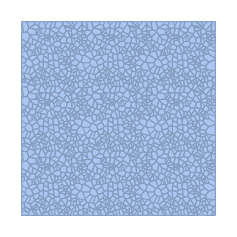

```mathematica
pts2=Flatten[Table[TranslationTransform[{2 i,2 j}][pts],{i,-1,1},{j,-1,1}],2];
vor=VoronoiMesh[pts2,{{-3,3},{-3,3}}]
```

```mathematica
vcells = Catenate[NearestMeshCells[{vor,2},#]&/@pts];
pvor = MeshRegion[MeshCoordinates[vor],MeshCells[vor,vcells]];
```

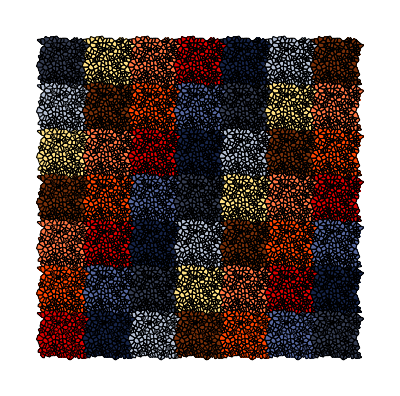

```mathematica
Show[Table[MeshRegion[TransformedRegion[pvor,TranslationTransform[{2 i,2 j}]],MeshCellStyle->{1->Black,2->ColorData[2,7 i+j+25]}],{i,-3,3},{j,-3,3}]]
```

```mathematica
vpts=Extract[MeshCoordinates[vor],Union@Flatten[MeshCells[vor,vcells]/.Polygon[x_]:>x]~Partition~1];
```

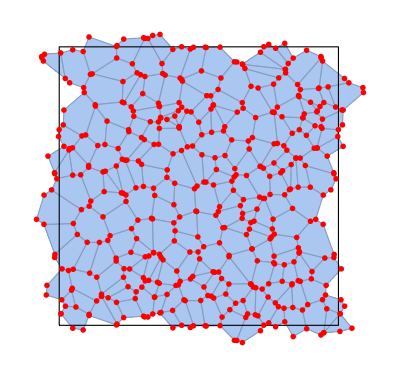

```mathematica
Show[pvor,Graphics[{{EdgeForm[{Thick,Dashed,Black}],FaceForm[None],Rectangle[{-1,-1},{1,1}]},Red,PointSize[0.01],Point@vpts}]]
```

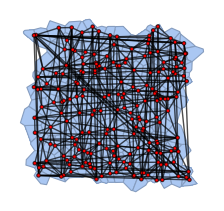

```mathematica
len=Length[pts];
C22=#.Transpose[#]&@vor["ConnectivityMatrix"[2,1]];
cells=Region`Mesh`MeshMemberCellIndex[vor,pts2][[All,2]];
C22perm=C22[[cells,cells]];
pC22=SparseArray[Unitize[Total[Partition[Unitize[C22perm],{len,len}],2]]];
pC22-=IdentityMatrix[len,SparseArray];
Show[pvor,Graph[AdjacencyGraph[pC22,VertexCoordinates->pts],VertexStyle->Red,EdgeStyle->Black]]
```

```mathematica
indToPtsAssoc=AssociationThread[
Replace[First@MeshCells[pvor],Point[x_]:>x,{1}]->
Replace[MeshPrimitives[pvor,0],Point->Sequence,{2},Heads->True]
];
```

```mathematica
ptsToIndAssoc=<|Reverse[Normal@indToPtsAssoc,2]|>;
```

```mathematica
cellVertexGrouping=AssociationThread[Range@Length[#]-> #]&@Replace[MeshCells[pvor,2],x_Polygon:>Sequence@@x,{1},Heads->True];
```

```mathematica
vertexCellAssoc=KeySort@GroupBy[Flatten[Thread[#]&/@Reverse[Normal@cellVertexGrouping,2]],First->Last];
```

```mathematica
wrappedMat=AssociationThread[Keys[cellVertexGrouping]-> Map[Lookup[indToPtsAssoc,#]/.periodicRules&,
Lookup[cellVertexGrouping,Keys[cellVertexGrouping]],{2}]];
```

```mathematica
faceListCoords=AssociationThread[Keys[cellVertexGrouping] ->Map[Lookup[indToPtsAssoc,#]&,Values@Normal@cellVertexGrouping]];
```

```mathematica
ptsToIndAssoc=KeyMap[SetPrecision[#,10]&,ptsToIndAssoc];
indToPtsAssoc=SetPrecision[#,10]&/@indToPtsAssoc;
wrappedMat=SetPrecision[#,10]&/@wrappedMat;
faceListCoords=SetPrecision[#,10]&/@faceListCoords;
```

## Main( )

```mathematica
(* rigid network parameter choices *)
```

```mathematica
ka=1000;
A0=0.01;
γ=0.04*ka*A0;
δt=0.001;
P0=0;
κ=0.025;
```

```mathematica
{γ/(ka*A0),κ/(ka*A0^(3/2) )}
```

{0.04,0.025}

```mathematica
indTopts=indToPtsAssoc;
ptsToInd=ptsToIndAssoc;
cellToVertexG=cellVertexGrouping;
vertexToCell=vertexCellAssoc;
$wrappedMat=wrappedMat;
$faceListCoords=faceListCoords;
areaPolygonAssoc=areaOfPolygon@faceListCoords;
periPolygonAssoc=perimeterOfPolygon@faceListCoords;
SeedRandom[1];
cj=0;
Tmax=4000;
t=0;
tt={};
Module[{cellsToRemove,edgechanged,polydiv,findEdges},
saveres=First@Last@Reap@Monitor[
While[t≤Tmax*δt,
cj=Round[t/δt];

(* T2 transitions *)
cellsToRemove=cellsforT2[areaPolygonAssoc,cellToVertexG];
If[cellsToRemove≠{},
{indTopts,ptsToInd,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords}=T2TransitionFn[cellsToRemove,indTopts,ptsToInd,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords];
];

(* T1 transitions *)
edges=DeleteDuplicatesBy[Flatten[Map[Partition[#,2,1,1]&,Values[cellToVertexG]],1],Sort];
{indTopts,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords}=T1transitionFn[edges,indTopts,ptsToInd,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords]; 
ptsToInd=AssociationMap[Reverse,indTopts];
areaPolygonAssoc=areaPolygon/@$faceListCoords;
periPolygonAssoc=perimeterPolygon/@$faceListCoords;

(* cell divisions *)
polydiv=selectDivCells[areaPolygonAssoc];
If[polydiv≠{},
Scan[({indTopts,cellToVertexG,areaPolygonAssoc,periPolygonAssoc}=cellDivision[#,indTopts,areaPolygonAssoc,periPolygonAssoc,cellToVertexG])&,polydiv];
vertexToCell=KeySort@GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
$faceListCoords=Lookup[indTopts,#]&/@cellToVertexG;
$wrappedMat=Map[#/.periodicRules&,$faceListCoords];
];
ptsToInd=AssociationMap[Reverse,indTopts];

(* update positions *)
localtopo=getLocalTopology[ptsToInd,indTopts,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords][#]&/@indTopts;
edgeLst=SortBy[Flatten[Map[Partition[#,2,1,1]&,Values[$faceListCoords]],1],First];
externedges=outeredges[indTopts,localtopo];
edgeLst=Join[edgeLst,externedges];
(*capture the first and the last output for the magnitude of force*)
If[cj==3||(cj+1)==Tmax,AppendTo[tt,Subscript[F, T][indTopts,ptsToInd,localtopo,areaPolygonAssoc,periPolygonAssoc,edgeLst]δt]];

indTopts=AssociationThread[Keys[indTopts]->SetPrecision[(Values[indTopts]+Subscript[F, T][indTopts,ptsToInd,localtopo,areaPolygonAssoc,periPolygonAssoc,edgeLst]δt),10]];

ptsToInd=AssociationMap[Reverse,indTopts];
$faceListCoords=Lookup[indTopts,#]&/@cellToVertexG;
areaPolygonAssoc=areaPolygon/@$faceListCoords;
periPolygonAssoc=perimeterPolygon/@$faceListCoords;
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
$wrappedMat=Map[#/.periodicRules&,$faceListCoords];
(*plt=Graphics[{ColorData[1][1],Thick,Values@Map[Line[Join[##,{First@#}]]&@Lookup[indTopts,#]&,cellToVertexG]},ImageSize->Medium];*)
plt=Graphics[{FaceForm[LightBlue],EdgeForm[{Black}],Values[Polygon@Lookup[indTopts,#]&/@cellToVertexG]},ImageSize->Medium];
(*plt=Graphics[{RGBColor[0.24720000000000014, 0.24, 0.6],Thick,Values@Map[Line[Join[##,{First@#}]]&@Lookup[indTopts,#]&,cellToVertexG]},ImageSize->Medium];*)
If[Mod[cj,2]==0,Sow[plt]];
t+=δt;
],{cj,plt}
]
];//AbsoluteTiming
```

{1639.97,Null}

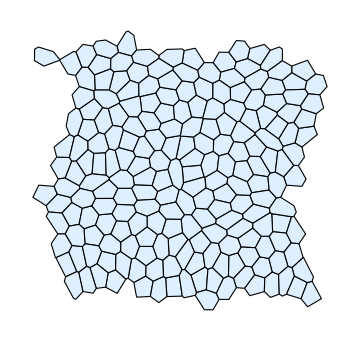

```mathematica
plt
```

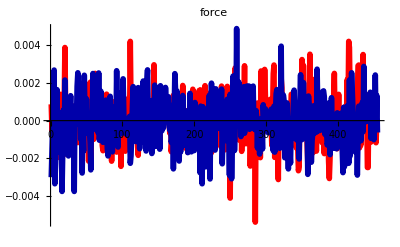
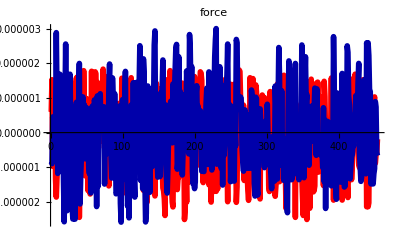

```mathematica
(ListLinePlot[#,PlotStyle->{{Thickness[0.01],Red},{Thickness[0.01],Darker@Blue}},PlotLabel->"force"]&)@*Transpose/@tt
```

```mathematica
(* different parameter choices *)
```

```mathematica
ka=1000;
A0=0.01;
γ=0.015*ka*A0;
P0=0;
κ=-0.025;
δt=0.00008;
```

```mathematica
{γ/(ka*A0),κ/(ka*A0^(3/2) )}
```

{0.015,-0.025}

```mathematica
indTopts=indToPtsAssoc;
ptsToInd=ptsToIndAssoc;
cellToVertexG=cellVertexGrouping;
vertexToCell=vertexCellAssoc;
$wrappedMat=wrappedMat;
$faceListCoords=faceListCoords;
areaPolygonAssoc=areaOfPolygon@faceListCoords;
periPolygonAssoc=perimeterOfPolygon@faceListCoords;
SeedRandom[1];
cj=0;
Tmax=4000;
t=0;
tt={};
Module[{cellsToRemove,edgechanged,polydiv,findEdges},
saveres=First@Last@Reap@Monitor[
While[t≤Tmax*δt,
cj=Round[t/δt];
(* T2 transitions *)
cellsToRemove=cellsforT2[areaPolygonAssoc,cellToVertexG];
If[cellsToRemove≠{},
{indTopts,ptsToInd,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords}=T2TransitionFn[cellsToRemove,indTopts,ptsToInd,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords];
];

(* T1 transitions *)
edges=DeleteDuplicatesBy[Flatten[Map[Partition[#,2,1,1]&,Values[cellToVertexG]],1],Sort];
{indTopts,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords}=T1transitionFn[edges,indTopts,ptsToInd,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords]; 
ptsToInd=AssociationMap[Reverse,indTopts];
areaPolygonAssoc=areaPolygon/@$faceListCoords;
periPolygonAssoc=perimeterPolygon/@$faceListCoords;

(* cell divisions *)
polydiv=selectDivCells[areaPolygonAssoc];
If[polydiv≠{},
Scan[({indTopts,cellToVertexG,areaPolygonAssoc,periPolygonAssoc}=cellDivision[#,indTopts,areaPolygonAssoc,periPolygonAssoc,cellToVertexG])&,polydiv];
vertexToCell=KeySort@GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
$faceListCoords=Lookup[indTopts,#]&/@cellToVertexG;
$wrappedMat=Map[#/.periodicRules&,$faceListCoords];
];
ptsToInd=AssociationMap[Reverse,indTopts];

(* update positions *)
localtopo=getLocalTopology[ptsToInd,indTopts,vertexToCell,cellToVertexG,$wrappedMat,$faceListCoords][#]&/@indTopts;
edgeLst=SortBy[Flatten[Map[Partition[#,2,1,1]&,Values[$faceListCoords]],1],First];
externedges=outeredges[indTopts,localtopo];
edgeLst=Join[edgeLst,externedges];
(*capture the first and the last output for the magnitude of force*)
If[cj==3||(cj+1)==Tmax,AppendTo[tt,Subscript[F, T][indTopts,ptsToInd,localtopo,areaPolygonAssoc,periPolygonAssoc,edgeLst]δt]];

indTopts=AssociationThread[Keys[indTopts]->SetPrecision[(Values[indTopts]+Subscript[F, T][indTopts,ptsToInd,localtopo,areaPolygonAssoc,periPolygonAssoc,edgeLst]δt),10]];

ptsToInd=AssociationMap[Reverse,indTopts];
$faceListCoords=Lookup[indTopts,#]&/@cellToVertexG;
areaPolygonAssoc=areaPolygon/@$faceListCoords;
periPolygonAssoc=perimeterPolygon/@$faceListCoords;
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertexG],First->Last];
$wrappedMat=Map[#/.periodicRules&,$faceListCoords];
(*plt=Graphics[{ColorData[1][1],Thick,Values@Map[Line[Join[##,{First@#}]]&@Lookup[indTopts,#]&,cellToVertexG]},ImageSize->Medium];*)
plt=Graphics[{FaceForm[LightBlue],EdgeForm[{Black}],Values[Polygon@Lookup[indTopts,#]&/@cellToVertexG]},ImageSize->Medium];
(*plt=Graphics[{RGBColor[0.24720000000000014, 0.24, 0.6],Thick,Values@Map[Line[Join[##,{First@#}]]&@Lookup[indTopts,#]&,cellToVertexG]},ImageSize->Medium];*)
If[Mod[cj,2]==0,Sow[plt]];
t+=δt;
],{cj,plt}
]
];//AbsoluteTiming
```

{1709.51,Null}

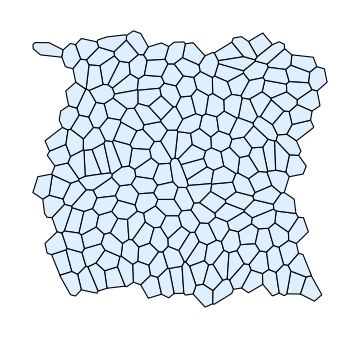

```mathematica
plt
```

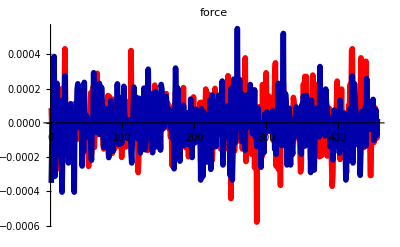
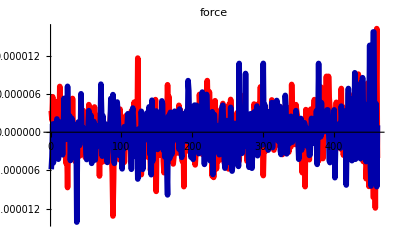

```mathematica
(ListLinePlot[#,PlotStyle->{{Thickness[0.01],Red},{Thickness[0.01],Darker@Blue}},PlotLabel->"force"]&)@*Transpose/@tt
```

## miscellaneous

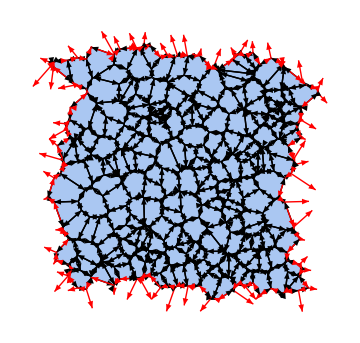

```mathematica
localtopotemp=getLocalTopology[ptsToIndAssoc,indToPtsAssoc,vertexCellAssoc,cellVertexGrouping,wrappedMat,faceListCoords][#]&/@indToPtsAssoc;
edgeLsttemp=SortBy[Flatten[Map[Partition[#,2,1,1]&,Values[faceListCoords]],1],First];
externedgestemp=outeredges[indToPtsAssoc,localtopotemp];
Show[pvor,Graphics[{{Thin,Black,Arrowheads[Small],Arrow/@edgeLsttemp},{Thin,Red,Arrowheads[Small],Arrow/@externedgestemp}}],ImageSize->Medium]
```